```mathematica
(*it somewhat improving accuracy by picking another sample data ,idk why*)
(*set directory for importing file*)
SetDirectory[NotebookDirectory[]];
myImport=Import["Fish.xlsx",{"Data",1}] [[3;;]];
```

```mathematica
(*transform into a list*)
```

```mathematica
myData=Thread[myImport[[1;;,1;;-2]]->myImport[[1;;,-1]]];
```

```mathematica
(*pick 80% of sample data from myData and 20% for evaluating*)
```

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

```mathematica
(*auto train*)
```

```mathematica
myPredict=Predict[myDataTrain]
```

PredictorFunction[…]

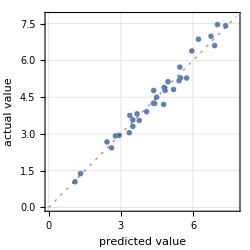
Predictor Measurements
Predictor method | LinearRegression
Number of test examples | 32
Standard deviation | 0.282 ± 0.031
Standard deviation baseline | 1.6 ± 0.18
R-squared | 0.969 ± 0.0099
Mean cross entropy | 0.224 ± 0.061
Single evaluation time | 5.99 ms/example
Batch evaluation speed | 892. examples/s
-Graphics- |

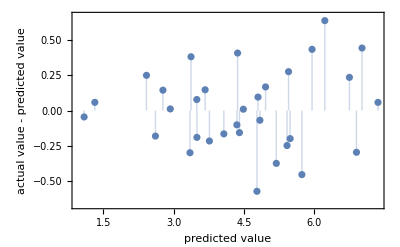

```mathematica
(*accuracy test*)
myAccuracy=PredictorMeasurements[myPredict,myDataTest];
myAccuracy["Report"]
myAccuracy/@{"ResidualPlot"}
```

```mathematica
(*save model *)
SetDirectory[NotebookDirectory[]];
DumpSave["trained_fish_price_predict.mx",myPredict];
```